```mathematica
(* 17.  Implement a Random walk in one dimension, which is the accumulated sum of random directions -1 and 1.  Display the results.  Do the same but where the directions are randomly chosen from square grid directions in 2D, and then do it on a hex grid.  Implement a random walk through the space of totalistic CA's, displaying their evolutions from a basic initial condition {{1},0} (compare p.391)*)
```

```mathematica
(* 1D Random Walk: I want to see the history evolution and not only the path in 1 dimension. So it is in 2D: it describes a 1D Random Walk in each time step. *)
```

```mathematica
step1D:=If[RandomInteger[]==0,-1,1]
```

```mathematica
RandomWalk1D[N_Integer]:= (steps1D= N; position= Round[N/2];
PadLeft[PadRight[{1},#],N+1]& /@  Table[position=position+step,{i,steps1D}]);
```

```mathematica
walk101=RandomWalk1D[100]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«98»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«47»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[walk101]
```

-Graphics-

```mathematica
walk1001=RandomWalk1D[1000]
```

{«1»}

```mathematica
ArrayPlot[walk1001]
```

-Graphics-

```mathematica
(* 2D Random Walk: it always starts in {0,0} and "passi" = steps *)
```

```mathematica
newxy[s_]:=(If[s==0,x=x+1,If[s==1,x=x-1,If[s==2,y=y+1,y=y-1]]];rw=Append[rw,{x,y}]);
```

```mathematica
costruisci[passi_Integer]:= (x=0;y=0;rw={{0,0}};newxy/@ Table[RandomInteger[3],{i,passi}] );
```

```mathematica
points[passi_Integer]:= (out=costruisci[passi];{Line[out],PointSize->Large,Point[{#1,#2}]& @@@ Last[out]});
```

```mathematica
grafica2D[passi_Integer]:= Graphics[{Blue,Thick,points[passi]},GridLines->Automatic,Frame->True,Axes->True]
```

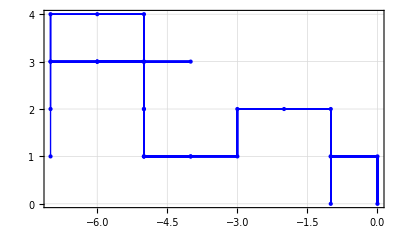

```mathematica
grafica2D[30]
```

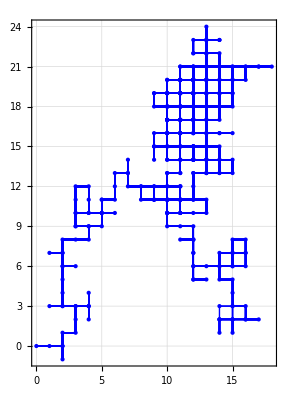

```mathematica
grafica2D[400]
```

```mathematica
grafica2D[800]
```

-Graphics-

```mathematica
(* Then I found this way a lot easier: For a hex grid: *)
```

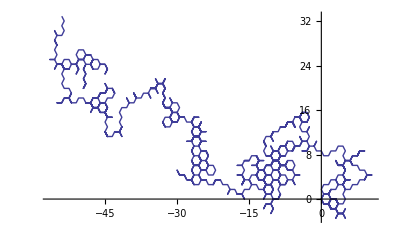

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[2]/3+π Mod[i,2]]],{i,1000}]]]
```

```mathematica
(* And than I used this method also for the sqared grid: *)
```

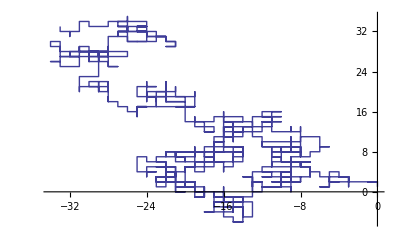

```mathematica
ListLinePlot[Accumulate[Table[Through[{Cos,Sin}[2 π RandomInteger[3]/4]],{1000}]]]
```

```mathematica
(* In this way I'll show the 1D random Walk in time (x axes)*)
```

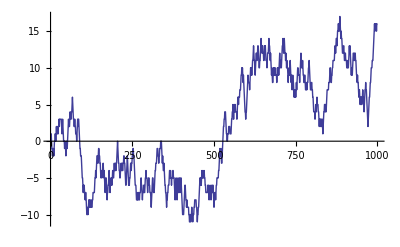

```mathematica
ListLinePlot[Accumulate @ RandomInteger[{-1,1},1000]]
```